# Instability Scale

The stability of Higgs potential requires that 2λ μ_S^2-A^2>0. As λ running to smaller value at high energy scale, this inequality may be violated.

```mathematica
ClearAll["Global`*"]
```

## SM parameters

Input the measured physical parameters in the SM.

```mathematica
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(2 √2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
κ=1/(16 π^2)(*Phase space factor*);
Nf=6;(*number of flavor why?*)
Ng=3;(*number of generation*)
z3=Zeta[3];
(*QCD*)
CA=3;(*Casimir operator Subscript[C, A]=Subscript[C, 2](adj)*)
CF=4/3;(*Casimir operator Subscript[C, F]=Subscript[C, 2](fund)*)
TR=1/2;(*Index Subscript[T, R](fund)*)
dR=3;(*dimension of representation, can be understood as color factor*)
SmoothUnitStep[x_]:=ArcTan[10x]/π+1/2;
```

## Running coupling

β functions for the couplings, including the SM gauge couplings, Higgs quartic coupling, top Yukawa and the new trilinear term A. The running of A is up to 1-loop. But we can also try to include the leading contribution in 2-loop: the top Yukawa contribution, to the running. In the next section, different approximations will be discussed.

```mathematica
βyt[λ_,yt_,g3_,g2_,g1_]=2 yt(κ yt^2(3/4+1/2 dR)+κ g3^2(-3CF)+3 κ^2 λ^2-6 κ^2 yt^2 λ+κ^2 yt^4(3/4-9/4 dR)+κ^2*g3^2*yt^2*(6*CF+5/2*CF*dR)+κ^2*g3^4*(-3/2*CF^2-97/6*CA*CF+10/3*Nf*TR*CF)+κ^3*λ^3*(-18)+κ^3*yt^2*λ^2*(285/8-45/4*dR)+κ^3*yt^4*λ*(63/2+45/2*dR)+κ^3*yt^6*(-345/32+107/32*dR+39/16*dR^2+9/4*z3+3/2*z3*dR)+κ^3*g3^2*yt^2*λ*(6*CF)+κ^3*g3^2*yt^4*(-57/2*CF-81/8*CF*dR)+κ^3*g3^4*yt^2*(471/16*CF^2-119/8*CF^2*dR+25*TR*CF+717/16*CA*CF+77/4*CA*CF*dR-33/4*Nf*TR*CF-4*Nf*TR*CF*dR-27*z3*CF^2+18*z3*CF^2*dR-27/2*z3*CA*CF-9*z3*CA*CF*dR)+κ^3*g3^6*(-129/2*CF^3+129/4*CA*CF^2-11413/108*CA^2*CF+46*Nf*TR*CF^2+556/27*Nf*CA*TR*CF+140/27*Nf^2*TR^2*CF-48*z3*Nf*TR*CF^2+48*z3*Nf*CA*TR*CF))+yt κ(-9/4 g2^2-17/12 g1^2)+yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45*Ng)-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-Ng)g2^4+9 g2^2 g3^2);

(*Beta function for the gauge coupliNgs*)
βg3[λ_,yt_,g3_,g2_,g1_]=2*g3*(+κ*g3^2*(-11/6*CA+2/3*Nf*TR)+κ^2*g3^2*yt^2*(-2*TR)+κ^2*g3^4*(-17/3*CA^2+2*Nf*TR*CF+10/3*Nf*CA*TR)+κ^3*g3^2*yt^4*(9/2*TR+7/2*TR*dR)+κ^3*g3^4*yt^2*(-3*TR*CF-12*CA*TR)+κ^3*g3^6*(-2857/108*CA^3-Nf*TR*CF^2+205/18*Nf*CA*TR*CF+1415/54*Nf*CA^2*TR-22/9*Nf^2*TR^2*CF-79/27*Nf^2*CA*TR^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_]=-g1^3 κ(-1/6-20/9*Ng)+g1^3 κ^2 5/3(199/30 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_]=-g2^3 κ(43/6-4/3*Ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);

(*Beta function for the quartic self-coupliNg of the sCAlar field*)
βλ[λ_,yt_,g3_,g2_,g1_]=2*(+κ*λ^2*(12)+κ*yt^2*λ*(2*dR)+κ*yt^4*(-dR)+κ^2*λ^3*(-156)+κ^2*yt^2*λ^2*(-24*dR)+κ^2*yt^4*λ*(-1/2*dR)+κ^2*yt^6*(5*dR)+κ^2*g3^2*yt^2*λ*(10*CF*dR)+κ^2*g3^2*yt^4*(-4*CF*dR)+κ^3*λ^4*(3588+2016*z3)+κ^3*yt^2*λ^3*(291*dR)+κ^3*yt^4*λ^2*(789/2*dR-36*dR^2+252*z3*dR)+κ^3*yt^6*λ*(-1881/8*dR+80*dR^2-66*z3*dR)+κ^3*yt^8*(13/2*dR-195/8*dR^2-12*z3*dR)+κ^3*g3^2*yt^2*λ^2*(-306*CF*dR+288*z3*CF*dR)+κ^3*g3^2*yt^4*λ*(895/4*CF*dR-324*z3*CF*dR)+κ^3*g3^2*yt^6*(-19/2*CF*dR+60*z3*CF*dR)+κ^3*g3^4*yt^2*λ*(-119/2*CF^2*dR+77*CA*CF*dR-16*Nf*TR*CF*dR+72*z3*CF^2*dR-36*z3*CA*CF*dR)+κ^3*g3^4*yt^4*(131/2*CF^2*dR+48*TR*CF*dR-109/2*CA*CF*dR+10*Nf*TR*CF*dR-48*z3*CF^2*dR+24*z3*CA*CF*dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10Ng)g2^4-39/4 g2^2 g1^2-(687/200+2Ng)25/9 g1^4)2λ+(497/8-8Ng)g2^6-(97/40+8/5 Ng)5/3 g2^4 g1^2-(717/200+8/5 Ng)25/9 g2^2 g1^4-(531/1000+24/25 Ng)125/27 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10*2 λ yt^2(17/12 g1^2+9/4 g2^2));
βA[λ_,yt_,g3_,g2_,g1_,A_]=2κ A(6 λ+3 yt^2+3 yb^2+yτ^2-9/4 g2^2-9/20 g1^2);(*dA/dlnμ=2 dA/dlnμ^2=(2 dm^2)/dlnμ^2 in the ref "Higgs near criticality..."*)
βAwithyt[λ_,yt_,g3_,g2_,g1_,A_]:=2κ A(6 λ+3 yt^2+3 yb^2+yτ^2-9/4 g2^2-9/20 g1^2)-2 κ^2 27/4 yt^4;(*dA/dlnμ=2 dA/dlnμ^2=(2 dm^2)/dlnμ^2*)
βμA[A_]:=κ A^2;(*Running of Subscript[μ, A]*)


(*gauge coupling*)
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;

mhpole=125.10+0.01*0;
mtpole=172.76+0.3;
αsmZ=0.1179+0.0010*(0);
g3mZ=√(4π*αsmZ);

(*MSbar quartic coupling*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);

(*MSbar Yukawa coupling*)ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);

g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;
```

## Scanning

We can scan over the physical parameter space m_S and sin θ. 
The running parameters are the bare parameters, which should be translated from the physical parameters. Furthermore, the bare parameter λ are redefined to match the SM measured Higgs vev and mass. This should be defined according to

4λ v^2(1+A^2/(8 λ^2 v^2))=m_h^2

The observed values are m_h and v, so the bare parameter λ at this renormalization scale should be derived from this equation. Now let’s write down these bare parameters as a function of the physical parameters.

But there is a problem that we would like to try: the measured value of λ, which is derived from the above equation, depends on the physical parameters m_S and sin θ. So during scanning, different parameter points correspond to different boundary condition being used to solve the running equations. How large is the impact of different boundary condition on λ?

Here we decided to try:
- Fixed boundary condition: always fix λ to be the SM value 0.13.
- Full expression of λ from the above equation.
- Use expression from the above equation, but take the linear expansion of the new-parameter-dependent part, given the assumption that A is small.

```mathematica
μS2[mS_,sinθ_]=mS^2(1-sinθ^2)+mhpole^2 sinθ^2;(*Bare parameter Subscript[μ, S]^2*)
A20[mS_,sinθ_]=((mhpole^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);(*Bare parameter A^2*)
λmeasure[mS_,sinθ_]=(λmtpole+√(λmtpole^2-2 A20[mS,sinθ]/v^2))/2;(*Measured value of λ from observed Subscript[m, h] and v, in full expression*)
λlinear[mS_,sinθ_]:=(λmtpole+λmtpole(1-A20[mS,sinθ]/(v^2 λmtpole^2)))/2;(*Take linear expansion on the A-dependent part of the above one*)
```

After defining the boundary conditions and the bare parameters, now we can solve the parameter runnings to find the instability scale. By default, the running of A is set up to 1-loop and the running of μ_S^2 is neglected. But we need to test these approximations.

### Default setting: A running up to 1-loop, full expression of λ boundary, neglect μ_S running

```mathematica
instable‵scale[mS_,sinθ_]:=(
λbound=λmeasure[mS,sinθ];
Abound=√A20[mS,sinθ];
sol:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hA'[t]==βA[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],hA[t]],hA[Log[mtpole/mZ]]==Abound,hλ[Log[mtpole/mZ]]==λbound,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt,hA},{t,-6,17*Log[10]},MaxSteps->10^5];
Afun[t_]:=(hA/.sol)[[1]][t];
yt[t_]:=(hyt/.sol)[[1]][t];
λ[t_]:=(hλ/.sol)[[1]][t];
g3[t_]:=(hg3/.sol)[[1]][t];
g2[t_]:=(hg2/.sol)[[1]][t];
g1[t_]:=(hg1/.sol)[[1]][t];
scale=x/.FindRoot[2μS2[mS,sinθ]*λ[Log[x/mZ]]-Afun[Log[x/mZ]]^2,{x,5}];
Log10[scale]
)
```

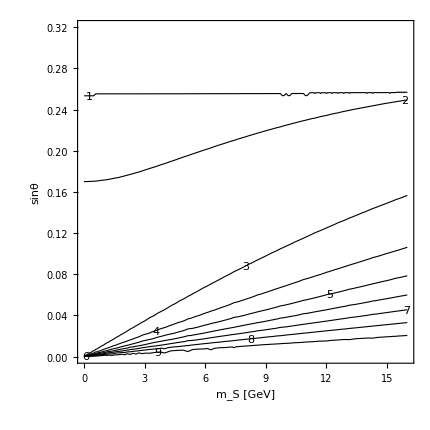

```mathematica
ContourPlot[instable‵scale[mS,sinθ],{mS,0,16},{sinθ,0,0.32},ContourLabels->True,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

### Use linear expanded expression for λ boundary condition

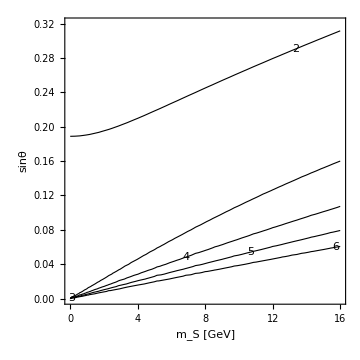

```mathematica
instable‵scale‵linear‵bound[mS_,sinθ_]:=(
λbound=λlinear[mS,sinθ];
Abound=√A20[mS,sinθ];
sol:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hA'[t]==βA[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],hA[t]],hA[Log[mtpole/mZ]]==Abound,hλ[Log[mtpole/mZ]]==λbound,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt,hA},{t,-6,17*Log[10]},MaxSteps->10^5];
Afun[t_]:=(hA/.sol)[[1]][t];
yt[t_]:=(hyt/.sol)[[1]][t];
λ[t_]:=(hλ/.sol)[[1]][t];
g3[t_]:=(hg3/.sol)[[1]][t];
g2[t_]:=(hg2/.sol)[[1]][t];
g1[t_]:=(hg1/.sol)[[1]][t];
scale=x/.FindRoot[2μS2[mS,sinθ]*λ[Log[x/mZ]]-Afun[Log[x/mZ]]^2,{x,5}];
Log10[scale]
)
ContourPlot[instable‵scale‵linear‵bound[mS,sinθ],{mS,0,16},{sinθ,0,0.32},ContourLabels->True,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

### Use fixed λ boundary condition

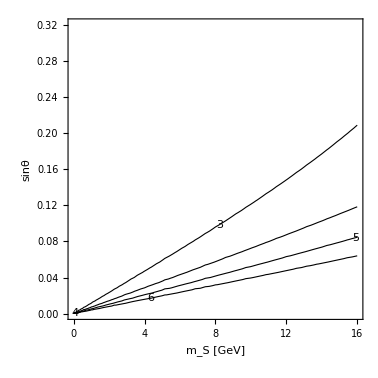

```mathematica
instable‵scale‵fix‵λbound[mS_,sinθ_]:=(
Abound=√A20[mS,sinθ];
sol:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hA'[t]==βA[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],hA[t]],hA[Log[mtpole/mZ]]==Abound,hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt,hA},{t,-6,17*Log[10]},MaxSteps->10^5];
Afun[t_]:=(hA/.sol)[[1]][t];
yt[t_]:=(hyt/.sol)[[1]][t];
λ[t_]:=(hλ/.sol)[[1]][t];
g3[t_]:=(hg3/.sol)[[1]][t];
g2[t_]:=(hg2/.sol)[[1]][t];
g1[t_]:=(hg1/.sol)[[1]][t];
scale=x/.FindRoot[2μS2[mS,sinθ]*λ[Log[x/mZ]]-Afun[Log[x/mZ]]^2,{x,5}];
Log10[scale]
)
ContourPlot[instable‵scale‵fix‵λbound[mS,sinθ],{mS,0,16},{sinθ,0,0.32},ContourLabels->True,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

### Include Top Yukawa contribution to the 2-loop running of A

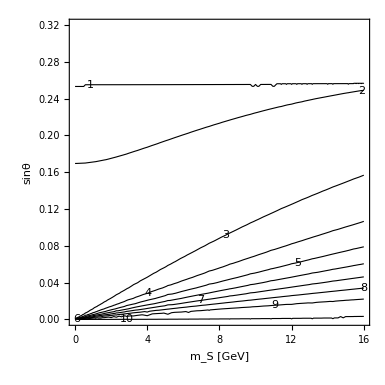

```mathematica
instable‵scale‵with‵ytA[mS_,sinθ_]:=(
λbound=λmeasure[mS,sinθ];
Abound=√A20[mS,sinθ];
sol:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hA'[t]==βAwithyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],hA[t]],hA[Log[mtpole/mZ]]==Abound,hλ[Log[mtpole/mZ]]==λbound,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt,hA},{t,-6,17*Log[10]},MaxSteps->10^5];
Afun[t_]:=(hA/.sol)[[1]][t];
yt[t_]:=(hyt/.sol)[[1]][t];
λ[t_]:=(hλ/.sol)[[1]][t];
g3[t_]:=(hg3/.sol)[[1]][t];
g2[t_]:=(hg2/.sol)[[1]][t];
g1[t_]:=(hg1/.sol)[[1]][t];
scale=x/.FindRoot[2μS2[mS,sinθ]*λ[Log[x/mZ]]-Afun[Log[x/mZ]]^2,{x,5}];
Log10[scale]
)
ContourPlot[instable‵scale‵with‵ytA[mS,sinθ],{mS,0,16},{sinθ,0,0.32},ContourLabels->True,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

### Include the running of μ_S

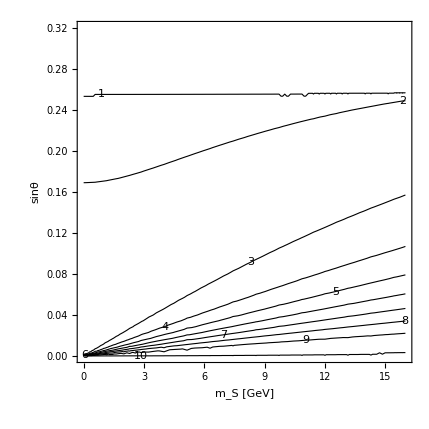

```mathematica
instable‵scale‵run‵μS[mS_,sinθ_]:=(
λbound=λmeasure[mS,sinθ];
Abound=√A20[mS,sinθ];
μSbound=μS2[mS,sinθ];
sol:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hA'[t]==βA[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],hA[t]],hμA'[t]==βμA[hA[t]],hA[Log[mtpole/mZ]]==Abound,hλ[Log[mtpole/mZ]]==λbound,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole,hμA[Log[mtpole/mZ]]==μSbound},{hg1,hg2,hg3,hλ,hyt,hA,hμA},{t,-6,17*Log[10]},MaxSteps->10^5];
Afun[t_]:=(hA/.sol)[[1]][t];
yt[t_]:=(hyt/.sol)[[1]][t];
λ[t_]:=(hλ/.sol)[[1]][t];
g3[t_]:=(hg3/.sol)[[1]][t];
g2[t_]:=(hg2/.sol)[[1]][t];
g1[t_]:=(hg1/.sol)[[1]][t];
μAfun[t_]:=(hμA/.sol)[[1]][t];
scale=x/.FindRoot[2μAfun[Log[x/mZ]]*λ[Log[x/mZ]]-Afun[Log[x/mZ]]^2,{x,5}];
Log10[scale]
)
ContourPlot[instable‵scale‵run‵μS[mS,sinθ],{mS,0,16},{sinθ,0,0.32},ContourLabels->True,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```